## Equations & Constants

```mathematica
ϵ0=8.85×10^-14(* Ф/см *);
q=1.6 10^-19(* Кл *);
η=1.3 (* Коэффициент влияния подложки *);
ϵox=4.;
nm=10^-7 (* нм *);
um=10^-4 (* мкм *);
Kg=8 10^12 (* 1/(cm^3 Rad) *);
```

```mathematica
△VT=(1/50 Fot q Kg dox η1)/Cox D;
μ=μ0/(1+θ (VG-VT)) (T0/T)^(3/2);
VT=VT0-α (T-T0)+△VT;
φt=T/11600.;
Cox=(ϵ0 ϵox)/dox;
Cd=η Cox;
Cit=q Dit;
S=φt Log[10] (1+(Cit+Cd)/Cox);
m=1+(Cit+Cd)/Cox;
ns=1/q (2 Cox m φt Log[1+Exp[(VG-VT)/(2 m φt)]])/(1+(2Cox)/Cd m Exp[-(VG-VT-Voff)/(2 m φt)]);
G=W/L μ q ns;



VDSAT=(q ns)/(Cox(1+η)); 
Id2=1/2 G VDSAT(1-Exp[(-2 Vd)/VDSAT]) ; (* version 1 *)



VDSAT1=(2 vmax L)/μ0 Tanh[(μ0 VDSAT)/(2 vmax L)];
IdVmax=1/2 G VDSAT1(1-Exp[(-2 Vd)/VDSAT1]) ; (* version 2 *)



Cch = Qc/(φd m+Qc/Cox) (* емкость канала *); 
μ0= 300;  (*подвижность электронов В/(см^2×с) *)
D0= 10;  (* коэффициент диффузии *)
φd = D0/μ0;
Qc0 =0.5 10^-13  ; (* общий заряд канала при нулевом смещении на стоке *); 

Qc= Qc0/2(1+Exp[-k/(1+ k) Vd/φd]) (* общий заряд канала от напряжения стока *); 

Idsat=Qc0/L vmax Tanh[(μ0 VDSAT)/(2 vmax L)]; (* version 3 *)(* обеспечивает аналитическое описание между двумя моделями насыщения *)
```

## Data

```mathematica
NpNVd50mV31C={{1.5,0.00127},{1.45,0.00116},{1.4,0.00105},{1.35,0.000932},{1.3,0.000809},{1.25,0.000683},{1.2,0.000558},{1.15,0.000433},{1.1,0.000313},{1.05,0.000205},{1.,0.000118},{0.95,0.0000575},{0.9,0.0000241},{0.85,8.69*^-6},{0.8,2.92*^-6},{0.75,9.63*^-7},{0.7,3.11*^-7},{0.65,1.*^-7},{0.6,3.28*^-8},{0.55,1.09*^-8},{0.5,3.61*^-9},{0.45,1.19*^-9},{0.4,3.33*^-10},{0.35,2.17*^-10},{0.3,2.17*^-10},{0.25,8.*^-11},{0.2,2.17*^-10}};
NpNVd50mV125C={{1.5,0.00106},{1.45,0.000997255},{1.4,0.0009237975},{1.35,0.000849839},{1.3,0.0007720475},{1.25,0.00069279},{1.2,0.00061373},{1.15,0.00053075749},{1.1,0.000448985},{1.05,0.0003669849},{1.,0.0002888749},{0.95,0.0002135775},{0.9,0.00014832},{0.85,0.00009434675},{0.8,0.00005448825},{0.75,0.00002895975},{0.7,0.00001416525},{0.65,6.537475*^-6},{0.6,2.951875*^-6},{0.55,1.3396*^-6},{0.5,5.8396*^-7},{0.45,2.4734*^-7},{0.4,9.869275*^-8},{0.35,2.7960749*^-8},{0.3,-3.165625*^-10},{0.25,-1.5047525*^-8},{0.2,-2.5886249*^-8}};
```

## Version 1

General::munfl: Exp[-1206.27] is too small to represent as a normalized machine number; precision may be lost.

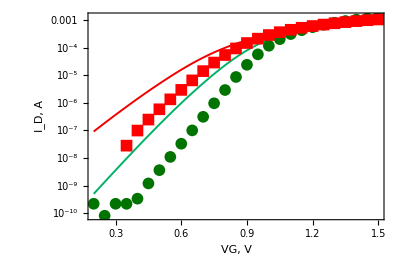

```mathematica
sub={Vd->0.05,Voff->0, α->0.002, μ0-> 275, dox-> 20 nm, W->1000 0.5 um, L-> 0.5 um, T0-> 300, VT0-> 0.7,Dit->1.5 10^12,θ-> 0.35};

Show[LogPlot[{Id2/.sub/.{D-> 0,T-> 304}, Id2/.sub/.{D-> 0,T-> 398}}, {VG, 0.2, 1.5}, PlotRange->{All, All},AspectRatio->0.65,GridLines->Automatic, PlotStyle->{{Thickness[0.0035], RGBColor[0.0, 0.7, 0.4]},{Thickness[0.0035], RGBColor[0.95, 0, 0]},{Thickness[0.0035], RGBColor[0, 0.0, 0.7]},{Thickness[0.0035], RGBColor[0.0, 0.8, 0.5]},{Thickness[0.0035], RGBColor[0.95, 0.2, 0.2]}}, Frame->True,  FrameLabel->{Style["VG, V", FontFamily->"Helvetica", FontSize->11, FontWeight->"Bold"],Style["I_D, A",FontFamily->"Helvetica", FontSize->11, FontWeight->"Bold"]}, BaseStyle->{11, FontFamily->"Helvetica"}],
ListLogPlot[{ NpNVd50mV31C ,NpNVd50mV125C },PlotRange->{All,All},AspectRatio->0.65,PlotStyle->{{PointSize[0.02],RGBColor [0, 0.45,0]},{PointSize[0.02],Red},{PointSize[0.02],RGBColor [0, 0,0.7]}},PlotMarkers->{Automatic,12},GridLines->Automatic, PlotRange->{All,All},Frame->True,FrameLabel->{Style["VG, V",FontFamily->"Helvetica",FontSize->11,FontWeight->"Bold"],Style[" Id, A",FontFamily->"Helvetica",FontSize->11,FontWeight->"Bold"]},BaseStyle->{11,FontFamily->"Helvetica"}]]
```

## Version 2

General::munfl: Exp[-1206.27] is too small to represent as a normalized machine number; precision may be lost.

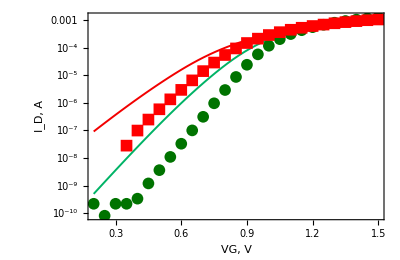

```mathematica
sub={Vd->0.05,Voff->0,α->0.002,  μ0-> 275, dox-> 20 nm, W->1000 0.5 um, L-> 0.5 um, T0-> 300, VT0-> 0.7,Dit->1.5 10^12,θ-> 0.35, D->0, vmax->1  10^7};
Show[LogPlot[{IdVmax/.sub/.{D-> 0,T-> 304},IdVmax/.sub/.{D-> 0,T-> 398}}, {VG, 0.2, 1.5}, PlotRange->{All, All},AspectRatio->0.65,GridLines->Automatic, PlotStyle->{{Thickness[0.0035], RGBColor[0.0, 0.7, 0.4]},{Thickness[0.0035], RGBColor[0.95, 0, 0]},{Thickness[0.0035], RGBColor[0, 0.0, 0.7]},{Thickness[0.0035], RGBColor[0.0, 0.8, 0.5]},{Thickness[0.0035], RGBColor[0.95, 0.2, 0.2]}}, Frame->True,  FrameLabel->{Style["VG, V", FontFamily->"Helvetica", FontSize->11, FontWeight->"Bold"],Style["I_D, A",FontFamily->"Helvetica", FontSize->11, FontWeight->"Bold"]}, BaseStyle->{11, FontFamily->"Helvetica"}],

ListLogPlot[{ NpNVd50mV31C, NpNVd50mV125C},PlotRange->{All,All},AspectRatio->0.65,PlotStyle->{{PointSize[0.01],RGBColor [0, 0.45,0]},{PointSize[0.01],Red},{PointSize[0.01],RGBColor [0, 0,0.7]}},PlotMarkers->{Automatic,12},GridLines->Automatic, PlotRange->{All,All},Frame->True,FrameLabel->{Style["VG, V",FontFamily->"Helvetica",FontSize->11,FontWeight->"Bold"],Style[" Id, A",FontFamily->"Helvetica",FontSize->11,FontWeight->"Bold"]},BaseStyle->{11,FontFamily->"Helvetica"}]]
```

```mathematica
Version 3
```

3 Version

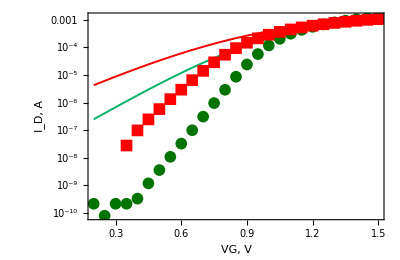

```mathematica
sub={Vd->0.05,Voff->0,α->0.002,  μ0-> 275, dox-> 20 nm, W->1000 0.5 um,L-> 0.5 um, T0-> 300, VT0-> 0.7,Dit->1.5 10^12,θ-> 0.35, D->0,k->0.01, vmax->1  10^7};

Show[LogPlot[{Idsat/.sub/.{D-> 0,T-> 304},Idsat/.sub/.{D-> 0,T-> 398}}, {VG, 0.2, 1.5}, PlotRange->{All, All},AspectRatio->0.65,GridLines->Automatic, PlotStyle->{{Thickness[0.0035], RGBColor[0.0, 0.7, 0.4]},{Thickness[0.0035], RGBColor[0.95, 0, 0]},{Thickness[0.0035], RGBColor[0, 0.0, 0.7]},{Thickness[0.0035], RGBColor[0.0, 0.8, 0.5]},{Thickness[0.0035], RGBColor[0.95, 0.2, 0.2]}}, Frame->True,  FrameLabel->{Style["VG, V", FontFamily->"Helvetica", FontSize->11, FontWeight->"Bold"],Style["I_D, A",FontFamily->"Helvetica", FontSize->11, FontWeight->"Bold"]}, BaseStyle->{11, FontFamily->"Helvetica"}],

ListLogPlot[{ NpNVd50mV31C, NpNVd50mV125C},PlotRange->{All,All},AspectRatio->0.65,PlotStyle->{{PointSize[0.01],RGBColor [0, 0.45,0]},{PointSize[0.01],Red},{PointSize[0.01],RGBColor [0, 0,0.7]}},PlotMarkers->{Automatic,12},GridLines->Automatic, PlotRange->{All,All},Frame->True,FrameLabel->{Style["VG, V",FontFamily->"Helvetica",FontSize->11,FontWeight->"Bold"],Style[" Id, A",FontFamily->"Helvetica",FontSize->11,FontWeight->"Bold"]},BaseStyle->{11,FontFamily->"Helvetica"}]]
```